```mathematica
Quit[]
```

```mathematica
SetDirectory["/Users/saraditsch/Desktop/Wtt/Mathematica"];
```

```mathematica
SetDirectory["/scratch/ge84fet/Wtt/Mathematica/MMatrix"];
```

```mathematica
$LoadAddOns = {"FeynArts"};
Quiet[Check[Get["FeynCalc`"],Print["FeynCalc is not available."]]]
$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[p4,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
MakeBoxes[p5,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(5\)]\)";
```

```mathematica
SetMandelstam[s,{p1,p2,p3,p4,p5},{0,0,SMP["m_t"],SMP["m_t"],SMP["m_W"]}];
Identities={s[1,5] -> 2SMP["m_t"]^2+SMP["m_W"]^2-s[1,2]-s[1,3]-s[1,4], s[2,5]-> 2SMP["m_t"]^2+SMP["m_W"]^2-s[1,2]-s[2,3]-s[2,4], s[3,5]-> 3SMP["m_t"]^2+SMP["m_W"]^2-s[1,3]-s[2,3]-s[3,4], s[4,5]-> 3SMP["m_t"]^2+SMP["m_W"]^2-s[1,4]-s[2,4]-s[3,4]}/.s[3,4]->-(s[2,4]+s[2,3]+s[1,4]+s[1,3]+s[1,2]-4*SMP["m_t"]^2-SMP["m_W"]^2);
AppendTo[Identities,s[3,4]->-(s[2,4]+s[2,3]+s[1,4]+s[1,3]+s[1,2]-4*SMP["m_t"]^2-SMP["m_W"]^2)];
Massless={SMP["m_d"]->0,SMP["m_u"]->0};
```

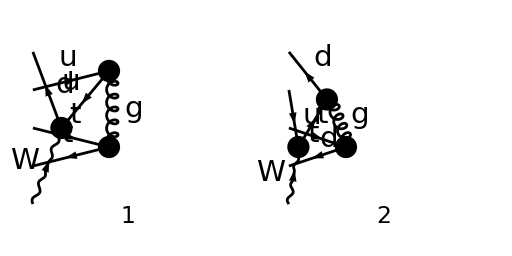

FeynArtsGraphics()(([1] | [2]))

```mathematica
diags=InsertFields[CreateTopologies[0,5->0],{-F[4,{1}],F[3,{1}],F[3,{3}],-F[3,{3}],V[3]}->{},InsertionLevel->{Classes},Model-> "SMQCD",ExcludeParticles->{S[_],V[3],V[1],V[2]}];
Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}]
```

```mathematica
diags=InsertFields[CreateTopologies[1,5->0],{-F[4,{1}],F[3,{1}],F[3,{3}],-F[3,{3}],V[3]}->{},InsertionLevel->{Classes},Model-> "SMQCD",ExcludeParticles->{S[_],V[3],V[1],V[2]}];
Paint[diags,ColumnsXRows->{4,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}]
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2,p3,p4,p5},OutgoingMomenta->{},ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,UndoChiralSplittings->True]//.Massless
```

Part::partw: Part 2 of {} does not exist.

(e g_s^2 T_Col1Col2^Glu6 T_Col4Col3^Glu6 (φ(-OverBar[p_4],m_t)).(γ̄)^Lor2.(φ(OverBar[p_3],m_t)) (φ(-OverBar[p_1])).(γ̄·ε̄(p_5)).(γ̄)^7.(γ̄·(OverBar[p_2]+OverBar[p_3]+OverBar[p_4])).(γ̄)^Lor2.(φ(OverBar[p_2])))/(√2 (sin(θ_W)) (-OverBar[p_3]-OverBar[p_4])^2 (-OverBar[p_2]-OverBar[p_3]-OverBar[p_4])^2)+(e g_s^2 T_Col1Col2^Glu6 T_Col4Col3^Glu6 (φ(-OverBar[p_4],m_t)).(γ̄)^Lor2.(φ(OverBar[p_3],m_t)) (φ(-OverBar[p_1])).(γ̄)^Lor2.(γ̄·(OverBar[p_2]+OverBar[p_5])).(γ̄·ε̄(p_5)).(γ̄)^7.(φ(OverBar[p_2])))/(√2 (sin(θ_W)) (-OverBar[p_2]-OverBar[p_5])^2 (-OverBar[p_3]-OverBar[p_4])^2)

```mathematica
ampSquared[0] = (1/2*1/3)^4*Simplify[(DoPolarizationSums[DiracSimplify[FermionSpinSum[(SUNSimplify[FeynAmpDenominatorExplicit[(1/SUNN^2)*(amp[0]*ComplexConjugate[amp[0]])], Explicit -> True, SUNNToCACF -> False])]], p5] //. Identities)//.Massless]
```

#### Compare Amplitude squared with Max

```mathematica
denumw={den[a_]->1/a};
MaxNotation={mw-> Sqrt[mwsq],mt-> Sqrt[mtsq],gW->gew,D->d};
rewriteCoupl={gs->Sqrt[4 Pi as],gW->Sqrt[4 Sqrt[2]*GF*mwsq]};
plugCoupl={as->0.118,GF->0.000116639};
```

```mathematica
plugMass={mtsq->29998.2,mwsq->6463.84,mzsq->8315.18};
plugKin1={s12->250000.,s13->-38312.6,s14->-111551.,s23->-110709.,s24->-36851.4,s34->173881.};
plugKin2= {s12->250000.,s13->-67762.,s14->-34739.5,s23->-61288.2,s24->-86750.3,s34->126997.};
```

```mathematica
amp=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/TreeLevelAmplitudeSquared.m"];
```

```mathematica
amp//Variables
```

{gs,gW,mt,D,mw,s12,s13,s14,s23,s24,den(2 mt^2+mw^2-s12-s13-s14),den(2 mt^2+mw^2-s12-s23-s24),den(4 mt^2+mw^2-s12-s13-s14-s23-s24)}

```mathematica
(amp//.denumw//.MaxNotation//.rewriteCoupl//.plugCoupl//.plugMass//.plugKin1)/0.10363683192986434
```

-2.12499

```mathematica
(amp//.denumw//.MaxNotation//.rewriteCoupl//.plugCoupl//.plugMass//.plugKin2)/0.05196298888664429
```

-2.12499

```mathematica
Sara=amp//.denumw//.MaxNotation//Together;
```

```mathematica
MaxD1=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Max/D1.m"];
MaxD2=Get["/Users/saraditsch/Desktop/Wtt/TreeLevelAmplitude/Max/D2.m"];
MaxNicer={diagid[a_]->1,cOlNA->1,cOlI2R->1};
Identities2={s15 -> 2*mt^2+mw^2-s12-s13-s14, s25-> 2mt^2+mw^2-s12-s23-s24, s35-> 3mt^2+mw^2-s13-s23-s34, s45-> 3mt^2+mw^2-s14-s24-s34}/.s34->-(s24+s23+s14+s13+s12-4*mt^2-mw^2);
AppendTo[Identities2,s34->-(s24+s23+s14+s13+s12-4*mt^2-mw^2)];
```

```mathematica
MaxDel=(MaxD1+MaxD2//.MaxNicer//.denumw//.Identities2//.MaxNotation)//Together;
```

```mathematica
Sara/MaxDel//Together
```

-2